```mathematica
f[x_]:=1/(1+x^2);
pts={-2,-1,0,1,2};
```

```mathematica
prod=Product[(x-pts[[i]]),{i,1,Length[pts]}]
```

(-2+x) (-1+x) x (1+x) (2+x)

```mathematica
num=prod/(x-pts)
```

{(-2+x) (-1+x) x (1+x),(-2+x) (-1+x) x (2+x),(-2+x) (-1+x) (1+x) (2+x),(-2+x) x (1+x) (2+x),(-1+x) x (1+x) (2+x)}

```mathematica
den=Table[num[[i]]/.{x->pts[[i]]},{i,1,Length[pts]}]
```

{24,-6,4,-6,24}

```mathematica
lag=num/den
```

{1/24 (-2+x) (-1+x) x (1+x),-1/6 (-2+x) (-1+x) x (2+x),1/4 (-2+x) (-1+x) (1+x) (2+x),-1/6 (-2+x) x (1+x) (2+x),1/24 (-1+x) x (1+x) (2+x)}

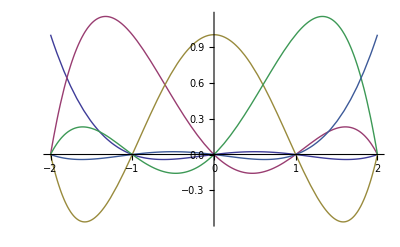

```mathematica
Plot[lag,{x,-2,2},PlotStyle->Thick]
```

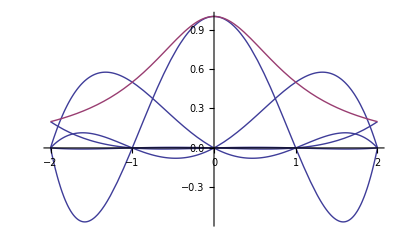

```mathematica
Plot[{lag*f[pts],f[x]},{x,-2,2}]
```

```mathematica
poly=Total[lag*f[pts]]
```

1/120 (-2+x) (-1+x) x (1+x)-1/12 (-2+x) (-1+x) x (2+x)+1/4 (-2+x) (-1+x) (1+x) (2+x)-1/12 (-2+x) x (1+x) (2+x)+1/120 (-1+x) x (1+x) (2+x)

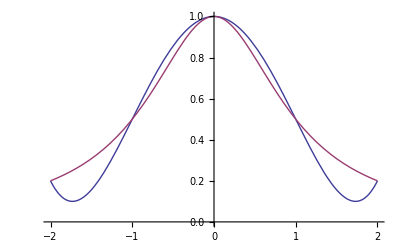

```mathematica
Plot[{poly,f[x]},{x,-2,2}]
```

```mathematica
f[x_]:=1/(1+x^2);
a=-1;
b=2;
n=10;
pts=Table[a+i*(b-a)/n,{i,0,n}]
```

{-1,-7/10,-2/5,-1/10,1/5,1/2,4/5,11/10,7/5,17/10,2}

```mathematica
prod=Product[(x-pts[[i]]),{i,1,Length[pts]}]
```

(-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x)

```mathematica
num=prod/(x-pts)
```

{(-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x),(-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (1+x),(-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (7/10+x) (1+x),(-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (2/5+x) (7/10+x) (1+x),(-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (1/10+x) (2/5+x) (7/10+x) (1+x),(-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x),(-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x),(-2+x) (-17/10+x) (-7/5+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x),(-2+x) (-17/10+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x),(-2+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x),(-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x)}

```mathematica
den=Table[num[[i]]/.{x->pts[[i]]},{i,1,Length[pts]}]
```

{33480783/1562500,-33480783/15625000,3720087/7812500,-11160261/62500000,1594323/15625000,-531441/6250000,1594323/15625000,-11160261/62500000,3720087/7812500,-33480783/15625000,33480783/1562500}

```mathematica
lag=num/den
```

{1/33480783 1562500 (-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x),-1/33480783 15625000 (-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (1+x),1/3720087 7812500 (-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (7/10+x) (1+x),-1/11160261 62500000 (-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (2/5+x) (7/10+x) (1+x),1/1594323 15625000 (-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (1/10+x) (2/5+x) (7/10+x) (1+x),-1/531441 6250000 (-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x),1/1594323 15625000 (-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x),-1/11160261 62500000 (-2+x) (-17/10+x) (-7/5+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x),1/3720087 7812500 (-2+x) (-17/10+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x),-1/33480783 15625000 (-2+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x),1/33480783 1562500 (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x)}

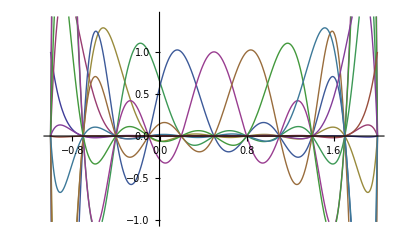

```mathematica
Plot[lag,{x,a,b},PlotStyle->Thick]
```

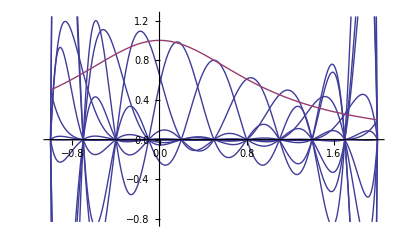

```mathematica
Plot[{lag*f[pts],f[x]},{x,a,b}]
```

```mathematica
poly=Total[lag*f[pts]]
```

1/33480783 781250 (-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x)-1/4988636667 1562500000 (-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (1+x)+1/107882523 195312500 (-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (7/10+x) (1+x)-1/1127186361 6250000000 (-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (2/5+x) (7/10+x) (1+x)+1/20726199 195312500 (-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (1/10+x) (2/5+x) (7/10+x) (1+x)-1/531441 5000000 (-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x)+1/65367243 390625000 (-2+x) (-17/10+x) (-7/5+x) (-11/10+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x)-1/2466417681 6250000000 (-2+x) (-17/10+x) (-7/5+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x)+1/137643219 97656250 (-2+x) (-17/10+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x)-1/13024024587 1562500000 (-2+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x)+1/33480783 312500 (-17/10+x) (-7/5+x) (-11/10+x) (-4/5+x) (-1/2+x) (-1/5+x) (1/10+x) (2/5+x) (7/10+x) (1+x)

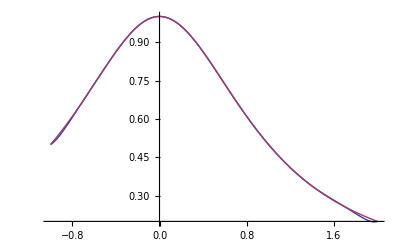

```mathematica
Plot[{poly,f[x]},{x,a,b}]
```